```mathematica
ClearAll["Global`*"]
```

```mathematica
Sample 0;
```

```mathematica
Ω0=RegionDifference[Rectangle[{-1,-1},{1,1}],Rectangle[{-1/2,-1/2},{1/2,1/2}]];
RegionPlot[Ω0];
NDSolveValue[{∇_{x,y}^2 u[x,y]==0,DirichletCondition[u[x,y]==100.,Abs[x]==1/2&&-1/2≤y≤1/2||-1/2≤x≤1/2&&Abs[y]==1/2],
DirichletCondition[u[x,y]==20.,Abs[x]==1||Abs[y]==1]},u,{x,y}∈Ω0];
Plot3D[%[x,y],{x,y}∈Ω0,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
RDiz[x_,y_]:=x+y+Sqrt[x^2+y^2]
RCon[x_,y_]:=-RDiz[-x,-y]
```

```mathematica
band[a_,x_]:=1/(2a)(a^2-x^2)
line[a_,b_,c_,x_,y_]:=(a x+b y +c)/Sqrt[a^2+b^2]
```

```mathematica
Geometry;
```

```mathematica
L=1;H=L;LPrime=L/L;HPrime=H/L;
ωH[x_,y_]:=x+LPrime/2;
ωC[x_,y_]:=LPrime/2-x;
(*ω1[x_,y_]:=band[LPrime/2,x]
ω2[x_,y_]:=band[HPrime/2,y]
ω[x_,y_]:=RCon[ω1[x,y],ω2[x,y]]*)

a=1;b=1;
ω1[x_,y_]:=x+a;
ω2[x_,y_]:=y+b;
ω3[x_,y_]:=a-x;
ω4[x_,y_]:=b-y;
ω12[x_,y_]:=RCon[ω1[x,y],ω2[x,y]]
ω34[x_,y_]:=RCon[ω3[x,y],ω4[x,y]]
ω[x_,y_]:=RCon[ω12[x,y],ω34[x,y]]
```

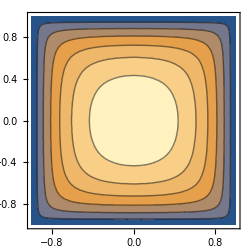

```mathematica
ContourPlot[ω[x,y],{x,-a,a},{y,-b,b},ImageSize->250]
```

```mathematica
Physical Parameters;
```

```mathematica
Tc=-1; Th=1; Pr=0.71; Ra=10^3; Gr=Ra/Pr; f1=Th; f2=Tc;
```

```mathematica
F[x_,y_]:=(f2 ω12[x,y]+f1 ω34[x,y])/(ω12[x,y]+ω34[x,y])
FModif[x_,y_]:=If[Abs[ω12[x,y]+ω34[x,y]]==0,(f1+f2)/2,F[x,y]]
```

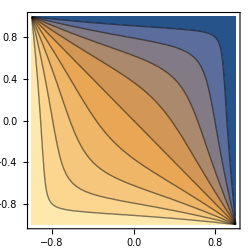
-Graphics--Graphics3D--Graphics3D-

```mathematica
Row@{
ContourPlot[F[x,y],{x,-a,a},{y,-b,b},ImageSize->250],
Plot3D[F[x,y],{x,-a,a},{y,-b,b},ColorFunction->"TemperatureMap",ImageSize->250],
Plot3D[FModif[x,y],{x,-a,a},{y,-b,b},ColorFunction->"TemperatureMap",ImageSize->250]
}
```

```mathematica
Ω[x_,y_]:=ω[x,y]F[x,y]
```

```mathematica
Row@{
Plot3D[Ω[x,y],{x,-a,a},{y,-b,b},ColorFunction->"TemperatureMap",ImageSize->250],Plot3D[ω[x,y]Ω[x,y],{x,-a,a},{y,-b,b},ColorFunction->"TemperatureMap",ImageSize->250]
}
```

-Graphics3D--Graphics3D-

```mathematica
Sample 2;
```

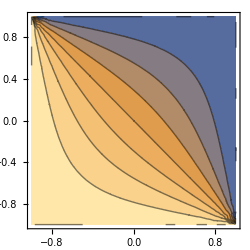
-Graphics--Graphics3D-

```mathematica
Ω1=Rectangle[{-1,-1},{1,1}];
RegionPlot[Ω1];

solFEM=NDSolveValue[{∇_{x,y}^2 u[x,y]==0,DirichletCondition[u[x,y]==Th,x==-1||y==-1],
DirichletCondition[u[x,y]==Tc,x==1||y==1]},u,{x,y}∈Ω1];
Row@{
ContourPlot[solFEM[x,y],{x,y}∈Ω1,Mesh->None,PlotRange->All,ImageSize->250],
Plot3D[solFEM[x,y],{x,y}∈Ω1,Mesh->None,PlotRange->All,ColorFunction->"TemperatureMap",ImageSize->250]
}
```

```mathematica
Sample 3;
```

```mathematica
tmp=Laplacian[F[x,y],{x,y}]//Simplify;
rhsF[x_,y_]:=If[(tmp//Denominator)==0,0.01,-tmp  ];
```

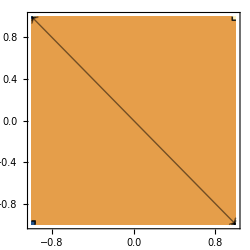
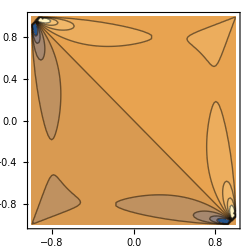
-Graphics--Graphics- -Graphics3D--Graphics3D-

```mathematica
Row@{
ContourPlot[rhsF[x,y],{x,-a,a},{y,-b,b},PlotRange->All,ImageSize->250],Plot3D[rhsF[x,y],{x,-a,a},{y,-b,b},PlotRange->All,ColorFunction->"TemperatureMap",ImageSize->250]
ContourPlot[rhsF[x,y]ω[x,y],{x,-a,a},{y,-b,b},PlotRange->All,ImageSize->250],Plot3D[rhsF[x,y]ω[x,y],{x,-a,a},{y,-b,b},PlotRange->All,ColorFunction->"TemperatureMap",ImageSize->250]
}
```

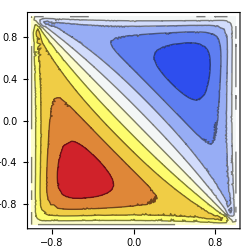
-Graphics--Graphics3D--Graphics3D-

```mathematica
sol00=NDSolveValue[{∇_{x,y}^2 u[x,y]==rhsF[x,y],DirichletCondition[u[x,y]==0,True]},u,{x,y}∈Ω1];
Row@{
ContourPlot[sol00[x,y],{x,y}∈Ω1,Mesh->None,PlotRange->All,ColorFunction->"TemperatureMap",ImageSize->250],
Plot3D[F[x,y]+sol00[x,y],{x,y}∈Ω1,Mesh->None,PlotRange->All,ColorFunction->"TemperatureMap",ImageSize->250],
Plot3D[{Abs[F[x,y]+sol00[x,y]-solFEM[x,y]]},{x,y}∈Ω1,Mesh->None,PlotRange->All,ColorFunction->"TemperatureMap",ImageSize->250]
}
```

```mathematica
NIntegrate[Sinc[x]^2,{x,0,π}]
```

1.41815

```mathematica
NIntegrate[(Sin[x]/x)^2,{x,0,π}]
```

1.41815

```mathematica
tmp
tmp//Denominator
```

-(4 (x+y) (14+x^2+y^2-6 √(2-2 x+x^2-2 y+y^2)-6 √(2+2 x+x^2+2 y+y^2)+√(2-2 x+x^2-2 y+y^2) √(2+2 x+x^2+2 y+y^2)))/(√(2-2 x+x^2-2 y+y^2) √(2+2 x+x^2+2 y+y^2) (-4+√(2-2 x+x^2-2 y+y^2)+√(2+2 x+x^2+2 y+y^2))^3)

√(2-2 x+x^2-2 y+y^2) √(2+2 x+x^2+2 y+y^2) (-4+√(2-2 x+x^2-2 y+y^2)+√(2+2 x+x^2+2 y+y^2))^3

```mathematica
rhsF2[x_,y_]:=If[(tmp//Denominator)==0,0.01,-tmp]
```

```mathematica
NIntegrate[ω[x,y]rhsF[x,y],{x,-1,1},{y,-1,1},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
```

1.95454

```mathematica
NIntegrate[ω[x,y]rhsF2[x,y],{x,-1,1},{y,-1,1},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
```

1.95155